```mathematica
ClearAll;Clear[x];Clear[y];Clear[w];
(**** ode generale, al variare di beta, gamma, eps ****)
Manipulate[s1=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.88,y[0]==-0.9,w[0]==0.99},{x,y,w},{t,500}];
s2=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.3015690815807199,y[0]==-0.9710846637966322,w[0]==-0.2876852798157373},{x,y,w},{t,500}];
s2bis=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.30,y[0]==-0.971,w[0]==-0.28},{x,y,w},{t,500}];
s2tris=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.32,y[0]==-0.95,w[0]==-0.25},{x,y,w},{t,500}];
s3=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.3015690815807199,y[0]==0.9710846637966322,w[0]==-0.2876852798157373},{x,y,w},{t,500}];
s3bis=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.30,y[0]==0.97,w[0]==-0.28},{x,y,w},{t,500}];
s3tris=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.33,y[0]==0.94,w[0]==-0.25},{x,y,w},{t,500}];
s4=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==1,y[0]==-1,w[0]==-1},{x,y,w},{t,500}];
s5 = NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-1,y[0]==1,w[0]==-1},{x,y,w},{t,500}];
ParametricPlot3D[{Evaluate[{x[t],y[t],w[t]}/.s1](*,Evaluate[{x[t],y[t],w[t]}/.s2],Evaluate[{x[t],y[t],w[t]}/.s2bis],Evaluate[{x[t],y[t],w[t]}/.s2tris],Evaluate[{x[t],y[t],w[t]}/.s3],Evaluate[{x[t],y[t],w[t]}/.s3bis],Evaluate[{x[t],y[t],w[t]}/.s3tris],Evaluate[{x[t],y[t],w[t]}/.s4],Evaluate[{x[t],y[t],w[t]}/.s5]*)},{t,0,500},PlotRange->{-1.1,1.1},AxesLabel->{"x","y","w"},  PlotStyle -> {Red,Green,Blue,Black, Purple}],{β,0,10},{ϵ,0,1},{γ,0,8}]
```

NDSolve::dsfun: 0.301569 cannot be used as a function.

General::stop: Further output of NDSolve::dsfun will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==1. (-0.971085)[0.0102143] Cosh[Times[«2»]]-2 0.301569[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. (-0.287685)[0.0102143] Sinh[Times[«2»]],0==-2 (-0.971085)[0.0102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],0==«1»,0.301569[0]==0.88,(-0.971085)[0]==-0.9,(-0.287685)[0]==0.99},{«1»},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==1. (-0.971085)[0.0102143] Cosh[Times[«2»]]-2 0.301569[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. (-0.287685)[0.0102143] Sinh[Times[«2»]],0==-2 (-0.971085)[0.0102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],0==«1»,0.301569[0]==0.88,(-0.971085)[0]==-0.9,(-0.287685)[0]==0.99},{«1»},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.301569[0]==0.88} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.301569[0]==0.301569} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.301569[0]==0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.301569[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.0102143]+1. Cosh[Times[«2»]] y[0.0102143],y'[0.0102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.0102143],w'[0.0102143]==«9»+2 Sinh[Times[«2»]] y[0.0102143],0.301569[0]==0.88,y[0]==-0.9,w[0]==0.99},{«19»,y,w},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.301569[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.0102143]+1. Cosh[Times[«2»]] y[0.0102143],y'[0.0102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.0102143],w'[0.0102143]==«9»+2 Sinh[Times[«2»]] y[0.0102143],0.301569[0]==0.88,y[0]==-0.9,w[0]==0.99},{«19»,y,w},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(**** ode generale a tempo invertito, calcolo manifold stabile dei punti fissi intermedi ****)
ClearAll; Clear[β]; Clear[ϵ]; Clear[γ];
Manipulate[s1=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.30,y[0]==0.97,w[0]==-0.2876852798157373},{x,y,w},{t,5}, MaxStepSize-> 0.0001];
s2=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.302,y[0]==0.9710846637966322,w[0]==-0.28},{x,y,w},{t,5},MaxStepSize-> 0.0001];
s2bis=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.3,y[0]==0.9710,w[0]==-0.287},{x,y,w},{t,5},MaxStepSize-> 0.0001];
s2tris=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.3,y[0]==0.9710846637966322,w[0]==-0.2876852798157373},{x,y,w},{t,5},MaxStepSize->0.0001];
s3=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.3015690815807,y[0]==0.98,w[0]==-0.29},{x,y,w},{t,5},MaxStepSize-> 0.0001];
s3bis=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.301,y[0]==0.97108,w[0]==-0.27},{x,y,w},{t,5},MaxStepSize-> 0.0001];
s3tris=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.307,y[0]==0.98,w[0]==-0.3},{x,y,w},{t,5},MaxStepSize-> 0.0001];
s4=NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.3,y[0]==0.95,w[0]==-0.26},{x,y,w},{t,5},MaxStepSize-> 0.0001];
s5 = NDSolve[{x'[t]==-(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==-(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==-(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.329,y[0]==0.95,w[0]==-0.2876852798157373},{x,y,w},{t,5},MaxStepSize-> 0.0001];
ParametricPlot3D[{Evaluate[{x[t],y[t],w[t]}/.s1],Evaluate[{x[t],y[t],w[t]}/.s2],Evaluate[{x[t],y[t],w[t]}/.s2bis],Evaluate[{x[t],y[t],w[t]}/.s2tris],Evaluate[{x[t],y[t],w[t]}/.s3],Evaluate[{x[t],y[t],w[t]}/.s3bis],Evaluate[{x[t],y[t],w[t]}/.s3tris],Evaluate[{x[t],y[t],w[t]}/.s4],Evaluate[{x[t],y[t],w[t]}/.s5]},{t,0,5},PlotRange->{-1.1,1.1},  PlotStyle -> {Red,Green,Blue,Black, Purple}, AxesLabel->{"x","y","w"}],{β,0,10},{ϵ,0,1},{γ,0,8}]
```

NDSolve::ndsz: At t == 0.2933, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.291602, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.292906, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.2933, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.291602, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.292906, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.2933, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.291602, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.292906, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.2933, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.291602, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.292906, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.2933, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.291602, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.292906, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.381773, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.343939, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.377036, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.733714, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.485594, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.642253, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.733714, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.485594, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.642253, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==-0.287685} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::ndode: The equations {0.568599[0]==-0.28} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287} are not differential equations or initial conditions in the dependent variables {x,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000102143]==-2 Sinh[Times[«2»]]+1. 0.568599[0.000102143] Sinh[Times[«2»]]+2 Cosh[Times[«2»]] x[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],0==-1. Cosh[Times[«2»]]+2 «19»[«23»] Cosh[Times[«2»]]+«2»+«1»-2 Sinh[Times[«2»]] y[0.000102143],«1»,y[0]==0.97,0.568599[0]==-0.287685},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000102143]==-2 Sinh[Times[«2»]]+1. 0.568599[0.000102143] Sinh[Times[«2»]]+2 Cosh[Times[«2»]] x[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],0==-1. Cosh[Times[«2»]]+2 «19»[«23»] Cosh[Times[«2»]]+«2»+«1»-2 Sinh[Times[«2»]] y[0.000102143],«1»,y[0]==0.97,0.568599[0]==-0.287685},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==-0.287685} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::ndode: The equations {0.568599[0]==-0.28} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287} are not differential equations or initial conditions in the dependent variables {x,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000102143]==-2 Sinh[Times[«2»]]+1. 0.568599[0.000102143] Sinh[Times[«2»]]+2 Cosh[Times[«2»]] x[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],0==-1. Cosh[Times[«2»]]+2 «19»[«23»] Cosh[Times[«2»]]+«2»+«1»-2 Sinh[Times[«2»]] y[0.000102143],«1»,y[0]==0.97,0.568599[0]==-0.287685},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000102143]==-2 Sinh[Times[«2»]]+1. 0.568599[0.000102143] Sinh[Times[«2»]]+2 Cosh[Times[«2»]] x[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],0==-1. Cosh[Times[«2»]]+2 «19»[«23»] Cosh[Times[«2»]]+«2»+«1»-2 Sinh[Times[«2»]] y[0.000102143],«1»,y[0]==0.97,0.568599[0]==-0.287685},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==-0.287685} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::ndode: The equations {0.568599[0]==-0.28} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287} are not differential equations or initial conditions in the dependent variables {x,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000102143]==-2 Sinh[Times[«2»]]+1. 0.568599[0.000102143] Sinh[Times[«2»]]+2 Cosh[Times[«2»]] x[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],0==-1. Cosh[Times[«2»]]+2 «19»[«23»] Cosh[Times[«2»]]+«2»+«1»-2 Sinh[Times[«2»]] y[0.000102143],«1»,y[0]==0.97,0.568599[0]==-0.287685},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000102143]==-2 Sinh[Times[«2»]]+1. 0.568599[0.000102143] Sinh[Times[«2»]]+2 Cosh[Times[«2»]] x[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],0==-1. Cosh[Times[«2»]]+2 «19»[«23»] Cosh[Times[«2»]]+«2»+«1»-2 Sinh[Times[«2»]] y[0.000102143],«1»,y[0]==0.97,0.568599[0]==-0.287685},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==-0.302} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.5[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.5[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.5,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.5[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.5[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.5,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndode: The equations {0.9[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.9[0]==-0.302} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.9[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.9[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.9[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.9,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.9[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.9[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.9,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==-0.302} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.5[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.5[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.5,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.5[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.5[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.5,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==-0.302} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.5[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.5[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.5,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.5[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.5[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{0.5,y,w},{0.000102143,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::dsfun: 0.301569 cannot be used as a function.

General::stop: Further output of NDSolve::dsfun will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-1. (-0.971085)[0.000102143] Cosh[Times[«2»]]+2 0.301569[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. (-0.287685)[0.000102143] Sinh[Times[«2»]],0==2 (-0.971085)[0.000102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],0==-1. Cosh[Times[«2»]]+«5»+«1»,«1»,(-0.971085)[0]==0.97,(-0.287685)[0]==-0.287685},«2»,«11»→«7»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-1. (-0.971085)[0.000102143] Cosh[Times[«2»]]+2 0.301569[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. (-0.287685)[0.000102143] Sinh[Times[«2»]],0==2 (-0.971085)[0.000102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],0==-1. Cosh[Times[«2»]]+«5»+«1»,«1»,(-0.971085)[0]==0.97,(-0.287685)[0]==-0.287685},«2»,«11»→«7»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndode: The equations {0.301569[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.301569[0]==-0.302} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.301569[0]==-0.3} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.301569[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.301569[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{«19»,y,w},{«23»,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==2 0.301569[0.000102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]]+1. Sinh[Times[«2»]] w[0.000102143]-1. Cosh[Times[«2»]] y[0.000102143],y'[0.000102143]==2 Sinh[Times[«2»]]+2 Cosh[Times[«2»]] y[0.000102143],w'[0.000102143]==-1. Cosh[Times[«2»]]+«6»,0.301569[0]==-0.3,y[0]==0.97,w[0]==-0.287685},{«19»,y,w},{«23»,5},MaxStepSize→0.0001]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.399517, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.415614, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.344679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
(**** ode generale, al variare di beta, gamma, eps ****)
Clear[x]; Clear[y];Clear[w];
Manipulate[s1=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]),y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.017,y[0]==-0.1,w[0]==0.1},{x,y,w},{t,500}];
Plot[{Evaluate[{x[t],y[t],w[t]}/.s1]},{t,0,500},PlotRange->{-1.1,1.1}, PlotStyle-> {Red,Blue,Green}],{β,0,10},{ϵ,0,1},{γ,0,8}]
```

NDSolve::ndode: The equations {0.5[0]==-0.017,0==-2 0.5[t] Cosh[1.5 0.5[t]]+2 Sinh[1.5 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],y'[0.0102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.0102143],w'[0.0102143]==-2 0.5[0.0102143] Sinh[Times[«2»]]-2 Cosh[Times[«2»]] w[0.0102143]-2 Cosh[Times[«2»]] w[0.0102143]+2 Sinh[Times[«2»]] y[0.0102143],0.5[0]==-0.017,y[0]==-0.1,w[0]==0.1},{0.5,y,w},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==-2. 0.5[0.0102143] Cosh[Times[«2»]]+2. Sinh[Times[«2»]],y'[0.0102143]==-2. Sinh[Times[«2»]]-2. Cosh[Times[«2»]] y[0.0102143],w'[0.0102143]==-2. 0.5[0.0102143] Sinh[Times[«2»]]-2. Cosh[Times[«2»]] w[0.0102143]-2. Cosh[Times[«2»]] w[0.0102143]+2. Sinh[Times[«2»]] y[0.0102143],0.5[0.]==-0.017,y[0.]==-0.1,w[0.]==0.1},{0.5,y,w},{0.0102143,500.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10.2143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[10.2143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],y'[10.2143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[10.2143],w'[10.2143]==-2 0.5[10.2143] Sinh[Times[«2»]]-2 Cosh[Times[«2»]] w[10.2143]-2 Cosh[Times[«2»]] w[10.2143]+2 Sinh[Times[«2»]] y[10.2143],0.5[0]==-0.017,y[0]==-0.1,w[0]==0.1},{0.5,y,w},{10.2143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.9[0]==-0.017,0==-2 0.9[t] Cosh[1.5 0.9[t]]+2 Sinh[1.5 0.9[t]]} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==-2 0.9[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],y'[0.0102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.0102143],w'[0.0102143]==-2 0.9[0.0102143] Sinh[Times[«2»]]-2 Cosh[Times[«2»]] w[0.0102143]-2 Cosh[Times[«2»]] w[0.0102143]+2 Sinh[Times[«2»]] y[0.0102143],0.9[0]==-0.017,y[0]==-0.1,w[0]==0.1},{0.9,y,w},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==-2. 0.9[0.0102143] Cosh[Times[«2»]]+2. Sinh[Times[«2»]],y'[0.0102143]==-2. Sinh[Times[«2»]]-2. Cosh[Times[«2»]] y[0.0102143],w'[0.0102143]==-2. 0.9[0.0102143] Sinh[Times[«2»]]-2. Cosh[Times[«2»]] w[0.0102143]-2. Cosh[Times[«2»]] w[0.0102143]+2. Sinh[Times[«2»]] y[0.0102143],0.9[0.]==-0.017,y[0.]==-0.1,w[0.]==0.1},{0.9,y,w},{0.0102143,500.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10.2143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.9[10.2143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],y'[10.2143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[10.2143],w'[10.2143]==-2 0.9[10.2143] Sinh[Times[«2»]]-2 Cosh[Times[«2»]] w[10.2143]-2 Cosh[Times[«2»]] w[10.2143]+2 Sinh[Times[«2»]] y[10.2143],0.9[0]==-0.017,y[0]==-0.1,w[0]==0.1},{0.9,y,w},{10.2143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsfun: 0.301569 cannot be used as a function.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==-2 0.301569[0.0102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]],0==-2 (-0.971085)[0.0102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],«2»,(-0.971085)[0]==-0.1,(-0.287685)[0]==0.1},{0.301569,-0.971085,-0.287685},{0.0102143,500}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10.2143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(* ode con b = g, eps = 0.5 *)
Manipulate[s=NDSolve[{x'[t]==-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+y[t] Cosh[β x[t]]- w[t] Sinh[β x[t]] ,y'[t]==-2 y[t]Cosh[β x[t]]-2 Sinh[β x[t]],
w'[t]==-2 w[t] Cosh[β x[t]]+ Cosh[β x[t]]-2 x[t] Sinh[β x[t]]- x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]],x[0]==-0.8,y[0]==0.8,w[0]==0.5},{x,y,w},{t,600}];Plot[{Evaluate[x[t]/.s]},{t,0,600},Frame-> True,PlotRange->{-1.1,1.1}],{β,0,10}]
```

NDSolve::ndode: The equations {0.57[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.57[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.57[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.57,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.57[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.57[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.57,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.57[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.57[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.57,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==0.5,0==1.-4. 0.568599[t]} are not differential equations or initial conditions in the dependent variables {x,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.0122571]==0.-2. x[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],0==1.-4. 0.568599[0.0122571],x[0]==-0.8,y[0]==0.8,0.568599[0]==0.5},{x,y,0.568599},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.0122571]==0.-2. x[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],0.==1.-4. 0.568599[0.0122571],x[0.]==-0.8,y[0.]==0.8,0.568599[0.]==0.5},{x,y,0.568599},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[12.2572]==0.-2. x[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],0==1.-4. 0.568599[12.2572],x[0]==-0.8,y[0]==0.8,0.568599[0]==0.5},{x,y,0.568599},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.5[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.5[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.5,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.5[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.5[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.5,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.5[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.5[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.5,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.301569[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.301569[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.301569[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.301569,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.301569[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.301569[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.301569,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.301569[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.301569[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.301569,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.9[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.9[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.9[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.9,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.9[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.9[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.9,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.9[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.9[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.9,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.5[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.5[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.5,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.5[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.5[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.5,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.5[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.5[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.5,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.5[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.5[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.5,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.5[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.5[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.5,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.5[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.5[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.5,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsfun: 0.301569 cannot be used as a function.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.+1. (-0.971085)[0.0122571]-2. 0.301569[0.0122571],0==0.-2. (-0.971085)[0.0122571],0==1.-4. (-0.287685)[0.0122571],0.301569[0]==-0.8,(-0.971085)[0]==0.8,(-0.287685)[0]==0.5},{0.301569,-0.971085,-0.287685},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.+1. (-0.971085)[0.0122571]-2. 0.301569[0.0122571],0.==0.-2. (-0.971085)[0.0122571],0.==1.-4. (-0.287685)[0.0122571],0.301569[0.]==-0.8,(-0.971085)[0.]==0.8,(-0.287685)[0.]==0.5},{0.301569,-0.971085,-0.287685},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.+1. (-0.971085)[12.2572]-2. 0.301569[12.2572],0==0.-2. (-0.971085)[12.2572],0==1.-4. (-0.287685)[12.2572],0.301569[0]==-0.8,(-0.971085)[0]==0.8,(-0.287685)[0]==0.5},{0.301569,-0.971085,-0.287685},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.301569[0]==-0.8} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.301569[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.301569[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.301569,y,w},{0.0122571,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0122571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.-2. 0.301569[0.0122571]+1. y[0.0122571],y'[0.0122571]==0.-2. y[0.0122571],w'[0.0122571]==1.-4. w[0.0122571],0.301569[0.]==-0.8,y[0.]==0.8,w[0.]==0.5},{0.301569,y,w},{0.0122571,600.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 12.2572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==0.-2. 0.301569[12.2572]+1. y[12.2572],y'[12.2572]==0.-2. y[12.2572],w'[12.2572]==1.-4. w[12.2572],0.301569[0]==-0.8,y[0]==0.8,w[0]==0.5},{0.301569,y,w},{12.2572,600}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(***** Troviamo tutti i punti fissi, al variare di beta, gamma ed eps ******)
(**** Il sistema completo dei punti fissi, risolto numericamente ****) 
Clear[b]; Clear[g];Clear[eps];
(** caso eps*g < 1 **)
b = 3; g = 1; eps = 0.5;
FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,1},{y,-1},{w,0.8}}]

b = 3; g = 1; eps = 0.5;
FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,-0.5},{y,0.5},{w,0.8}}]
```

{x→0.985975,y→-0.755641,w→-0.742341}

{x→-0.985975,y→0.755641,w→-0.742341}

```mathematica
(** caso eps*g > 1 **)
b = 2.1; g = 7; eps = 0.5;
FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,1},{y,1},{w,0.7}}]

b = 2.1; g = 7; eps = 0.5;
vettore=FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,0.5},{y,0.5},{w,0.7}}]
```

{x→0.834815,y→-0.999983,w→-0.834801}

{x→0.569016,y→-0.999306,w→-0.568599}

```mathematica
(* questa è l'equazione per la m_x col giusto segno *)
f[x_,β_,ϵ_,γ_] = -(x*(1-ϵ*Sinh[γ*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x]) - ϵ^2*Sinh[β*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x])) - Tanh[β*x] + ϵ*Tanh[γ*x] - ϵ*Tanh[γ*x]*Tanh[β*x]*Sinh[β*x]/(Cosh[γ*x] + Cosh[β*x]) + ϵ^2*Cosh[β*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x]));
```

```mathematica
Manipulate[Plot[f[x,β,eps,γ],{x,-1,1},Frame-> True,PlotRange->{-1.1,1.1}],{β,0,10},{eps,0,1},{γ,0,10}]
```

```mathematica
(****** Caso gamma = beta, eps = 0.5, il sistema di equazioni completo per i p.ti fissi, risolto numericamente ********)
b= 2.0; (* osservazione: ci sono (almeno) 5 soluzioni per valori di beta intorno a 2! *)
FindRoot[x ==(1/2 - 1/2 w)Tanh[b*x] && y == - Tanh[b*x] && w == -3/4 x Tanh[b*x] - 1/2 (Tanh[b*x])^2 +1/4,{{x,-0.5},{w,0.5},{y,0.5}}]

FindRoot[x ==(1/2 - 1/2 w)Tanh[b*x] && y == - Tanh[b*x] && w == -3/4 x Tanh[b*x] - 1/2 (Tanh[b*x])^2 +1/4,{{x,1},{w,1},{y,1}}]

FindRoot[x ==(1/2 - 1/2 w)Tanh[b*x] && y == - Tanh[b*x] && w == -3/4 x Tanh[b*x] - 1/2 (Tanh[b*x])^2 +1/4,{{x,0},{w,1},{y,0}}]

FindRoot[x ==(1/2 - 1/2 w)Tanh[b*x] && y == - Tanh[b*x] && w == -3/4 x Tanh[b*x] - 1/2 (Tanh[b*x])^2 +1/4,{{x,-1},{w,1},{y,1}}]

FindRoot[x ==(1/2 - 1/2 w)Tanh[b*x] && y == - Tanh[b*x] && w == -3/4 x Tanh[b*x] - 1/2 (Tanh[b*x])^2 +1/4,{{x,0.5},{w,0.5},{y,0.5}}]
```

{x→-0.467875,w→-0.276144,y→0.733263}

{x→0.780935,w→-0.705614,y→-0.915723}

{x→0.,w→0.25,y→0.}

{x→-0.780935,w→-0.705614,y→0.915723}

{x→0.467875,w→-0.276144,y→-0.733263}

```mathematica
0.942791601901231
```

0.942792

```mathematica
(*** Nel caso beta = gamma, eps = 0.5 ***)
Clear[b]; Clear[x];  (* l'equazione per la f[m_x] = 0, anche qui vediamo 5 punti di intersezione intorno a b = 2 *)
f[x_,b_] = (3*Tanh[b*x] + 2*(Tanh[b*x])^3)/(8 - 3(Tanh[b*x])^2)- x;
Manipulate[Plot[f[x,b],{x,-1,1},Frame-> True,PlotRange->{-1,1}],{b,0,10}]
```

```mathematica
ϵ = 0.5; γ = 7; β = 2;
VectorPlot3D[{-2 x Cosh[β x]+2 Sinh[β x]+2 ϵ y Cosh[β x]-2 ϵ w Sinh[β x],-2 y Cosh[γ x]-2 Sinh[γ x], -2 w Cosh[γ x]+2 ϵ Cosh[β x]-2 x Sinh[γ x]- 2ϵ x Sinh[β x]-2 w Cosh[β x]+2 y Sinh[β x]},{x,-1,1},{y,-1,1},{w,-1,1}]
```

-Graphics3D-

```mathematica
(*** calcolo autovalori nei punti fissi intermedi instabili ***)
b =2.1; g = 7; eps = 0.5; Clear[x];Clear[y];Clear[w];
vettore=FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,0.57},{y,-0.9},{w,-0.55}}]
M = {{D[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x],x],D[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x],y],D[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x],w]} ,{D[-2*y*Cosh[g*x] - 2*Sinh[g*x],x] ,D[-2*y*Cosh[g*x] - 2*Sinh[g*x],y],D[-2*y*Cosh[g*x] - 2*Sinh[g*x],w]},{D[-2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x],x],D[-2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x],y],D[-2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x],w]}}/.x->vettore[[1]][[2]] /.y->vettore[[2]][[2]]/.w->vettore[[3]][[2]];
Eigenvalues[M]
```

{x→0.569016,y→-0.999306,w→-0.568599}

{-58.8033,-53.6989,0.876483}

```mathematica
(*** calcolo autovalori nei punti fissi esterni stabili ***)
Clear[x];Clear[y];Clear[w];
b = 2.; g = 7; eps = 0.5;
vettore=FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,0.5},{y,-1},{w,0.7}}]
M = {{D[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x],x],D[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x],y],D[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x],w]} ,{D[-2*y*Cosh[g*x] - 2*Sinh[g*x],x] ,D[-2*y*Cosh[g*x] - 2*Sinh[g*x],y],D[-2*y*Cosh[g*x] - 2*Sinh[g*x],w]},{D[-2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x],x],D[-2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x],y],D[-2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x],w]}}/.x->vettore[[1]][[2]] /.y->vettore[[2]][[2]]/.w->vettore[[3]][[2]];
Eigenvalues[M]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.711178,y→-0.999944,w→-0.711083}

{-151.567,-145.226,-1.76575×10^-7}

```mathematica
b =2; g = 7; eps = 0.5;
val = Table[0,{iter,1,26}];
For[i = 1, i ≤ 26, i++,
b = b + 0.1;
vettore=FindRoot[-2*x*Cosh[b*x] + 2*Sinh[b*x] + 2*eps*y*Cosh[b*x] - 2*eps*w*Sinh[b*x] == 0 && -2*y*Cosh[g*x] - 2*Sinh[g*x] == 0 && -2*w*Cosh[g*x] - 2*x*Sinh[g*x] - 2*w*Cosh[b*x] + 2*y*Sinh[b*x] + 2*eps*Cosh[b*x] -2*eps*x*Sinh[b*x]==0,{{x,0.4},{y,-0.85},{w,0.7}}];
val[[i]] = {vettore[[1]][[2]],vettore[[2]][[2]],vettore[[3]][[2]]}
]
```

```mathematica
val
ListPointPlot3D[val]
```

{{0.569016,-0.999306,-0.568599},{0.497052,-0.998101,-0.496006},{0.446836,-0.996168,-0.444834},{0.407471,-0.993361,-0.404119},{0.374944,-0.989552,-0.369786},{0.347201,-0.984631,-0.339721},{0.323012,-0.978503,-0.312639},{0.301569,-0.971085,-0.287685},{0.282309,-0.962304,-0.264255},{0.264821,-0.952098,-0.241901},{0.248794,-0.940407,-0.220286},{0.233985,-0.927178,-0.199148},{0.220203,-0.912359,-0.178282},{0.207292,-0.895899,-0.157526},{0.195122,-0.877744,-0.13675},{0.183585,-0.857836,-0.115853},{0.172586,-0.836109,-0.0947535},{0.162043,-0.812486,-0.0733888},{0.151881,-0.786874,-0.0517099},{0.142032,-0.759159,-0.0296802},{0.13243,-0.729196,-0.00727311},{0.123008,-0.696801,0.0155292},{0.113698,-0.66173,0.0387375},{0.104423,-0.623653,0.0623564},{0.0950939,-0.582116,0.0863851},{3.47845×10^-20,-2.43491×10^-19,0.25}}

-Graphics3D-

```mathematica
(*** calcolo del punto a_c ***)
Clear[ϵ];Clear[γ];Clear[β];
(* questa è l'equazione per la m_x col giusto segno *)
f[x_,β_,ϵ_,γ_] = -(x*(1-ϵ*Sinh[γ*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x]) - ϵ^2*Sinh[β*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x])) - Tanh[β*x] + ϵ*Tanh[γ*x] - ϵ*Tanh[γ*x]*Tanh[β*x]*Sinh[β*x]/(Cosh[γ*x] + Cosh[β*x]) + ϵ^2*Cosh[β*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x]));
h[x_,β_,ϵ_,γ_] = D[f[x, β,ϵ,γ],x];
(*ϵ= 0.5;γ=7; 
Reduce[f[x,β,ϵ,γ] == 0 && h[x,β,ϵ,γ] ==0,{x,β}]*)

Clear[ϵ];Clear[γ];Clear[β];
Reduce[f[x,β,0.5,β] == 0 && h[x,β,0.5,β] ==0,{x,β}]

(*b =1; g = 7; eps = 0.5;
val = Table[0,{iter,1,260}];
For[i = 1, i ≤ 260, i++,
b = b + 0.01;
vettore=FindRoot[f[x,β,ϵ,γ] == 0 && h[x_,β_,ϵ_,γ_] ==0,{{x,0.4},{y,-0.85},{w,0.7}}];
val[[i]] = {vettore[[1]][[2]],vettore[[2]][[2]],vettore[[3]][[2]]}
]*)
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[-(0.25 Sinh[x])/(Cosh[x]+Cosh[7 x])+Tanh[x]-x (1-(0.25 Sinh[x] Tanh[x])/(Cosh[x]+Cosh[7 x])-(0.5 Sinh[7 x] Tanh[x])/(Cosh[x]+Cosh[7 x]))-0.5 Tanh[7 x]+(0.5 Sinh[x] Tanh[x] Tanh[7 x])/(Cosh[x]+Cosh[7 x])==0&&-1-(0.25 Cosh[x])/(Cosh[x]+Cosh[7 x])+Sech[x]^2-3.5 Sech[7 x]^2+(0.25 Sinh[x] (Sinh[x]+7 Sinh[7 x]))/(Cosh[x]+Cosh[7 x])^2+(0.25 Sinh[x] Tanh[x])/(Cosh[x]+Cosh[7 x])+(3.5 Sech[7 x]^2 Sinh[x] Tanh[x])/(Cosh[x]+Cosh[7 x])+(0.5 Sinh[7 x] Tanh[x])/(Cosh[x]+Cosh[7 x])-x (-(0.25 Sinh[x])/(Cosh[x]+Cosh[7 x])-(0.5 Sech[x]^2 Sinh[7 x])/(Cosh[x]+Cosh[7 x])-(3.5 Cosh[7 x] Tanh[x])/(Cosh[x]+Cosh[7 x])-(0.25 Sech[x] Tanh[x])/(Cosh[x]+Cosh[7 x])+(0.25 Sinh[x] (Sinh[x]+7 Sinh[7 x]) Tanh[x])/(Cosh[x]+Cosh[7 x])^2+(0.5 Sinh[7 x] (Sinh[x]+7 Sinh[7 x]) Tanh[x])/(Cosh[x]+Cosh[7 x])^2)+(0.5 Sinh[x] Tanh[7 x])/(Cosh[x]+Cosh[7 x])+(0.5 Sech[x] Tanh[x] Tanh[7 x])/(Cosh[x]+Cosh[7 x])-(0.5 Sinh[x] (Sinh[x]+7 Sinh[7 x]) Tanh[x] Tanh[7 x])/(Cosh[x]+Cosh[7 x])^2==0,{x,β}]

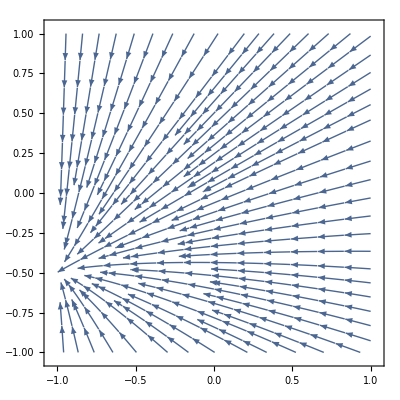

```mathematica
(*** StreamPlot delle proiezioni del campo per trovare la varietà stabile ***) 
Clear[x];Clear[y];Clear[w];
ϵ = 0.5; γ = 7; β = 2.1;x=0.5;
StreamPlot[{-2 y Cosh[γ x]-2 Sinh[γ x], -2 w Cosh[γ x]+2 ϵ Cosh[β x]-2 x Sinh[γ x]- 2ϵ x Sinh[β x]-2 w Cosh[β x]+2 y Sinh[β x]},{y,-1,1},{w,-1,1}]
```

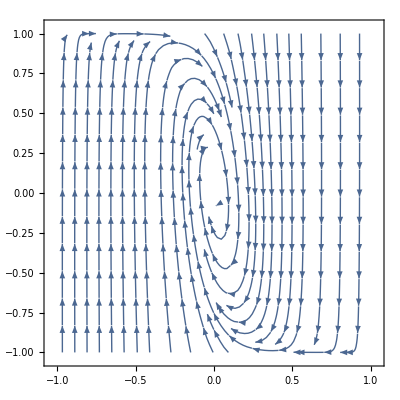

```mathematica
ϵ = 0.5; γ = 7; β = 2.1;w=0.5685992471224048;
StreamPlot[{-2 x Cosh[β x]+2 Sinh[β x]+2 ϵ y Cosh[β x]-2 ϵ w Sinh[β x],-2 y Cosh[γ x]-2 Sinh[γ x]},{x,-1,1},{y,-1,1}]
```

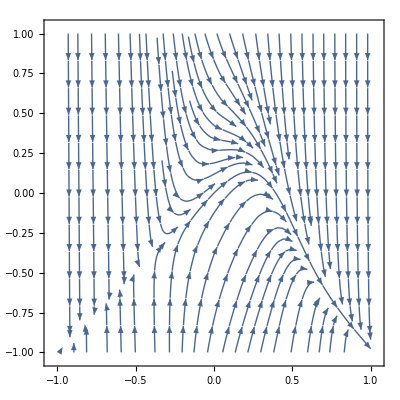

```mathematica
ϵ = 0.5; γ = 7; β = 2.1;y=0.999;
StreamPlot[{-2 x Cosh[β x]+2 Sinh[β x]+2 ϵ y Cosh[β x]-2 ϵ w Sinh[β x],-2 w Cosh[γ x]+2 ϵ Cosh[β x]-2 x Sinh[γ x]- 2ϵ x Sinh[β x]-2 w Cosh[β x]+2 y Sinh[β x]},{x,-1,1},{w,-1,1}]
```

```mathematica
(****** plots per l'articolo *****)
f[x_,β_,ϵ_,γ_] = -(x*(1-ϵ*Sinh[γ*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x]) - ϵ^2*Sinh[β*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x])) - Tanh[β*x] + ϵ*Tanh[γ*x] - ϵ*Tanh[γ*x]*Tanh[β*x]*Sinh[β*x]/(Cosh[γ*x] + Cosh[β*x]) + ϵ^2*Cosh[β*x]*Tanh[β*x]/(Cosh[γ*x] + Cosh[β*x]));

P= Plot[{f[x,1,0.5,1],f[x,1.71,0.5,1],f[x,2.5,0.5,1]}, {x,-1,1}, Frame -> False, PlotRange ->{-0.5,0.5}, PlotStyle -> {Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotStyle-> {Red,Blue,Green}, PlotLabels-> {"beta = 1","beta = 1.71","beta = 2.5"},AxesLabel->{"x","f(x)"}]
```

-Graphics-

```mathematica
Export["/Users/guglielmo/Desktop/Desktop/bautin/grafico_f.jpg",P];
```

```mathematica
P2= Plot[{f[x,1,0.5,7],f[x,2,0.5,7],f[x,2.5,0.5,7]}, {x,-1,1}, Frame -> False, PlotRange ->{-0.5,0.5}, PlotStyle -> {Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotStyle-> {Red,Blue,Green}, PlotLabels-> {"beta = 1","beta = 2","beta = 2.5"},AxesLabel->{"x","f(x)"}]

P3 = Plot[{f[x,3,0.5,7],f[x,5.14,0.5,7], f[x,7,0.5,7]},{x,-1,1}, Frame -> False, PlotRange ->{-0.5,0.5}, PlotStyle -> {Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotStyle-> {Yellow,Blue,Green}, PlotLabels-> {"beta = 3","beta = 5.14","beta = 7"},AxesLabel->{"x","f(x)"}]
```

-Graphics-

-Graphics-

```mathematica
Export["/Users/guglielmo/Desktop/Desktop/bautin/grafico_f_over1.jpg",P2];
Export["/Users/guglielmo/Desktop/Desktop/bautin/grafico_f_over2.jpg",P3];
```

```mathematica
(**** Plots per l'articolo: ode generale, al variare di beta, gamma, eps ****)
(** dati iniziali vicini a 0, beta = 1 **)
Clear[x]; Clear[y];Clear[w]; ϵ = 0.5;γ = 7; β = 2.3;
Q1 = Manipulate[s1=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]),y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.5,y[0]==-0.7,w[0]==0.5},{x,y,w},{t,50}];
Plot[{Evaluate[{x[t],y[t],w[t]}/.s1]},{t,0,50},PlotRange->{-1.1,1.1}, PlotStyle-> {Red,Blue,Green},PlotStyle -> {Thickness[0.005],Thickness[0.005],Thickness[0.005]}, AxesLabel-> {"t",""}]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==0.5},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2. Sinh[Times[«2»]]-2. ϵ Sinh[Times[«2»]] w[0.00102143]-2. Cosh[Times[«2»]] x[0.00102143]+2. ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0.]==0.5},{x,y,w},{0.00102143,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[1.02143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[1.02143]-2 Cosh[Times[«2»]] x[1.02143]+2 ϵ Cosh[Times[«2»]] y[1.02143],«4»,w[0]==0.5},{x,y,w},{1.02143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==0.5} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.5,y[0]==-0.7,w[0]==0.5},{0.5,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==-2. 0.5[0.00102143] Cosh[Times[«2»]]+2. Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2. Sinh[Times[«2»]]-2. Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2. Sinh[Times[«2»]] y[0.00102143],0.5[0.]==0.5,y[0.]==-0.7,w[0.]==0.5},{0.5,y,w},{0.00102143,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[1.02143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[1.02143]+1. Cosh[Times[«2»]] y[1.02143],y'[1.02143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[1.02143],«2»,y[0]==-0.7,w[0]==0.5},{0.5,y,w},{1.02143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==0.5,0.5[0]==0.5} are not differential equations or initial conditions in the dependent variables {y}.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. 0.568599[0.00102143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],0==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.5,y[0]==-0.7,0.568599[0]==0.5},{0.5,y,0.568599},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==-2. 0.5[0.00102143] Cosh[Times[«2»]]+2. Sinh[Times[«2»]]-1. 0.568599[0.00102143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2. Sinh[Times[«2»]]-2. Cosh[Times[«2»]] y[0.00102143],0.==«9»+2. Sinh[Times[«2»]] y[0.00102143],0.5[0.]==0.5,y[0.]==-0.7,0.568599[0.]==0.5},{«1»},{0.00102143,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[1.02143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. 0.568599[1.02143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[1.02143],y'[1.02143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[1.02143],0==«9»+2 Sinh[Times[«2»]] y[1.02143],0.5[0]==0.5,y[0]==-0.7,0.568599[0]==0.5},{0.5,y,0.568599},{1.02143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.999[0]==-0.7,0.5[0]==0.5,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==-2. 0.5[0.00102143] Cosh[Times[«2»]]+1. 0.999[0.00102143] Cosh[Times[«2»]]+2. Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143],0.==-2. 0.999[0.00102143] Cosh[Times[«2»]]-2. Sinh[Times[«2»]],w'[0.00102143]==«1»,0.5[0.]==0.5,0.999[0.]==-0.7,w[0.]==0.5},{0.5,0.999,w},{0.00102143,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==0.5},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2. Sinh[Times[«2»]]-2. ϵ Sinh[Times[«2»]] w[0.00102143]-2. Cosh[Times[«2»]] x[0.00102143]+2. ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0.]==0.5},{x,y,w},{0.00102143,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[1.02143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[1.02143]-2 Cosh[Times[«2»]] x[1.02143]+2 ϵ Cosh[Times[«2»]] y[1.02143],«4»,w[0]==0.5},{x,y,w},{1.02143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.301569[0]==0.5} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==-2. 0.301569[0.00102143] Cosh[Times[«2»]]+2. Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2. Sinh[Times[«2»]]-2. Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2. Sinh[Times[«2»]] y[0.00102143],0.301569[0.]==0.5,y[0.]==-0.7,w[0.]==0.5},{«19»,y,w},{«22»,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.301569[1.02143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[1.02143]+1. Cosh[Times[«2»]] y[1.02143],y'[1.02143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[1.02143],w'[1.02143]==«9»+2 Sinh[Times[«2»]] y[1.02143],0.301569[0]==0.5,y[0]==-0.7,w[0]==0.5},{0.301569,y,w},{1.02143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(**** Plots per l'articolo: 3D simulation ****)
ClearAll;Clear[x];Clear[y];Clear[w];β = 5.3; ϵ = 0.5; γ = 7;
(**** ode generale, al variare di beta, gamma, eps ****)
Manipulate[s1=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.88,y[0]==-0.9,w[0]==-0.99},{x,y,w},{t,50}];
s2=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.1,y[0]==-0.2,w[0]==-0.2876852798157373},{x,y,w},{t,50}];
s2bis=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==0.32,y[0]==-0.9710846637966322,w[0]==-0.2876852798157373},{x,y,w},{t,50}];
s2tris=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.32,y[0]==0.9710846637966322,w[0]==-0.2876852798157373},{x,y,w},{t,50}];
s3=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.3015690815807199,y[0]==0.9710846637966322,w[0]==-0.2876852798157373},{x,y,w},{t,50}];
s3bis=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.30,y[0]==0.97,w[0]==-0.28},{x,y,w},{t,50}];
s3tris=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.33,y[0]==0.94,w[0]==-0.25},{x,y,w},{t,50}];
s4=NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==1,y[0]==-1,w[0]==-1},{x,y,w},{t,50}];
s5 = NDSolve[{x'[t]==(-2 x[t] Cosh[β x[t]]+2 Sinh[β x[t]]+2 ϵ y[t] Cosh[β x[t]]-2 ϵ w[t] Sinh[β x[t]]) ,y'[t]==(-2 y[t]Cosh[γ x[t]]-2 Sinh[γ x[t]]),
w'[t]==(-2 w[t] Cosh[γ x[t]]+2 ϵ Cosh[β x[t]]-2 x[t] Sinh[γ x[t]]- 2ϵ x[t]Sinh[β x[t]]-2 w[t] Cosh[β x[t]]+2 y[t] Sinh[β x[t]]),x[0]==-0.9,y[0]==1,w[0]==-1},{x,y,w},{t,50}];
ParametricPlot3D[{Evaluate[{x[t],y[t],w[t]}/.s1],Evaluate[{x[t],y[t],w[t]}/.s2],Evaluate[{x[t],y[t],w[t]}/.s2bis],Evaluate[{x[t],y[t],w[t]}/.s2tris],(*Evaluate[{x[t],y[t],w[t]}/.s3],Evaluate[{x[t],y[t],w[t]}/.s3bis],Evaluate[{x[t],y[t],w[t]}/.s3tris],Evaluate[{x[t],y[t],w[t]}/.s4]*)Evaluate[{x[t],y[t],w[t]}/.s5]},{t,0,50},PlotRange->{-1.1,1.1},AxesLabel->{"x","y","w"},PlotStyle -> {{Red,Thickness[0.009]},{Green,Thickness[0.009]},{Blue,Thickness[0.009]},{Orange,Thickness[0.009]}, {Black,Thickness[0.009]}}]]
```

NDSolve::ndode: The equations {0.5[0]==0.88} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==0.1} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==0.32} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,w[0]==-0.99},{0.5,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,w[0]==-0.99},{0.5,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.5[0]==0.88} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==0.1} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.5[0]==0.32} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,w[0]==-0.99},{0.5,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],w'[0.00102143]==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,w[0]==-0.99},{0.5,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==-0.99,0.5[0]==0.88} are not differential equations or initial conditions in the dependent variables {y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287685,0.5[0]==0.1} are not differential equations or initial conditions in the dependent variables {y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287685,0.5[0]==0.32} are not differential equations or initial conditions in the dependent variables {y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. 0.568599[0.00102143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],0==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,0.568599[0]==-0.99},{0.5,y,0.568599},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. 0.568599[0.00102143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],0==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,0.568599[0]==-0.99},{0.5,y,0.568599},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.568599[0]==-0.99,0.5[0]==0.88} are not differential equations or initial conditions in the dependent variables {y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287685,0.5[0]==0.1} are not differential equations or initial conditions in the dependent variables {y}.

NDSolve::ndode: The equations {0.568599[0]==-0.287685,0.5[0]==0.32} are not differential equations or initial conditions in the dependent variables {y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. 0.568599[0.00102143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],0==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,0.568599[0]==-0.99},{0.5,y,0.568599},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. 0.568599[0.00102143] Sinh[Times[«2»]]+1. Cosh[Times[«2»]] y[0.00102143],y'[0.00102143]==-2 Sinh[Times[«2»]]-2 Cosh[Times[«2»]] y[0.00102143],0==«9»+2 Sinh[Times[«2»]] y[0.00102143],0.5[0]==0.88,y[0]==-0.9,0.568599[0]==-0.99},{0.5,y,0.568599},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.999[0]==-0.9,0.5[0]==0.88,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

NDSolve::ndode: The equations {0.999[0]==-0.2,0.5[0]==0.1,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

NDSolve::ndode: The equations {0.999[0]==-0.971085,0.5[0]==0.32,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+1. 0.999[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143],0==-2 0.999[0.00102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],w'[0.00102143]==1. Cosh[Times[«2»]]-1. 0.5[0.00102143] Sinh[Times[«2»]]+«7»,0.5[0]==0.88,0.999[0]==-0.9,w[0]==-0.99},{0.5,0.999,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+1. 0.999[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143],0==-2 0.999[0.00102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],w'[0.00102143]==1. Cosh[Times[«2»]]-1. 0.5[0.00102143] Sinh[Times[«2»]]+«7»,0.5[0]==0.88,0.999[0]==-0.9,w[0]==-0.99},{0.5,0.999,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.999[0]==-0.9,0.5[0]==0.88,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

NDSolve::ndode: The equations {0.999[0]==-0.2,0.5[0]==0.1,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

NDSolve::ndode: The equations {0.999[0]==-0.971085,0.5[0]==0.32,0==-2 0.999[t] Cosh[7 0.5[t]]-2 Sinh[7 0.5[t]]} are not differential equations or initial conditions in the dependent variables {w}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+1. 0.999[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143],0==-2 0.999[0.00102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],w'[0.00102143]==1. Cosh[Times[«2»]]-1. 0.5[0.00102143] Sinh[Times[«2»]]+«7»,0.5[0]==0.88,0.999[0]==-0.9,w[0]==-0.99},{0.5,0.999,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==-2 0.5[0.00102143] Cosh[Times[«2»]]+1. 0.999[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. Sinh[Times[«2»]] w[0.00102143],0==-2 0.999[0.00102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],w'[0.00102143]==1. Cosh[Times[«2»]]-1. 0.5[0.00102143] Sinh[Times[«2»]]+«7»,0.5[0]==0.88,0.999[0]==-0.9,w[0]==-0.99},{0.5,0.999,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsfun: 0.301569 cannot be used as a function.

General::stop: Further output of NDSolve::dsfun will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==1. (-0.971085)[0.00102143] Cosh[Times[«2»]]-2 0.301569[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. (-0.287685)[0.00102143] Sinh[Times[«2»]],0==-2 (-0.971085)[0.00102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],0==«1»,0.301569[0]==0.88,(-0.971085)[0]==-0.9,(-0.287685)[0]==-0.99},«1»,{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0==1. (-0.971085)[0.00102143] Cosh[Times[«2»]]-2 0.301569[0.00102143] Cosh[Times[«2»]]+2 Sinh[Times[«2»]]-1. (-0.287685)[0.00102143] Sinh[Times[«2»]],0==-2 (-0.971085)[0.00102143] Cosh[Times[«2»]]-2 Sinh[Times[«2»]],0==«1»,0.301569[0]==0.88,(-0.971085)[0]==-0.9,(-0.287685)[0]==-0.99},«1»,{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndode: The equations {0.301569[0]==0.88} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.301569[0]==0.1} are not differential equations or initial conditions in the dependent variables {w,y}.

NDSolve::ndode: The equations {0.301569[0]==0.32} are not differential equations or initial conditions in the dependent variables {w,y}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.00102143]==2 Sinh[Times[«2»]]-2 ϵ Sinh[Times[«2»]] w[0.00102143]-2 Cosh[Times[«2»]] x[0.00102143]+2 ϵ Cosh[Times[«2»]] y[0.00102143],«4»,w[0]==-0.99},{x,y,w},{0.00102143,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

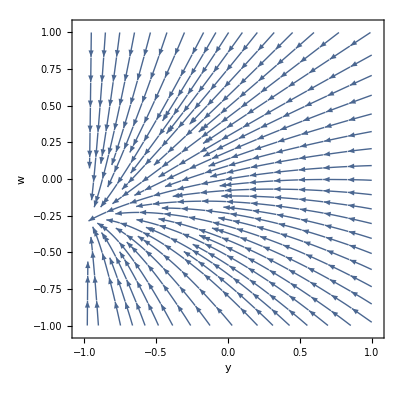

```mathematica
(*** StreamPlot delle proiezioni del campo per trovare la varietà stabile ***) 

Clear[x];Clear[y];Clear[w];
ϵ = 0.5; γ = 7; β = 2.8;x=0.3015690815807199;
StreamPlot[{-2 y Cosh[γ x]-2 Sinh[γ x], -2 w Cosh[γ x]+2 ϵ Cosh[β x]-2 x Sinh[γ x]- 2ϵ x Sinh[β x]-2 w Cosh[β x]+2 y Sinh[β x]},{y,-1,1},{w,-1,1}, FrameLabel-> {"y","w"}]
```

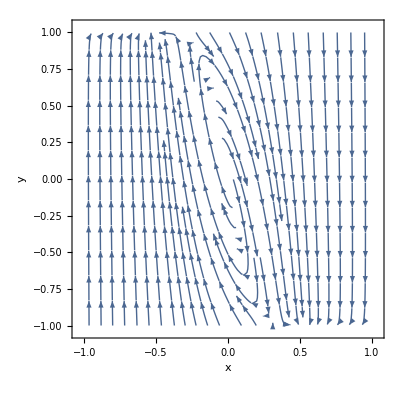

```mathematica
ϵ = 0.5; γ = 7; β = 2.8;w=-0.2876852798157373;
StreamPlot[{-2 x Cosh[β x]+2 Sinh[β x]+2 ϵ y Cosh[β x]-2 ϵ w Sinh[β x],-2 y Cosh[γ x]-2 Sinh[γ x]},{x,-1,1},{y,-1,1}, FrameLabel-> {"x","y"}]
```

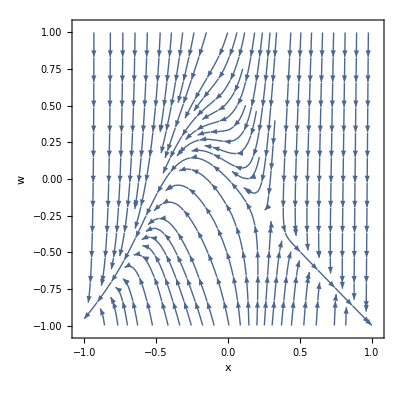

```mathematica
ϵ = 0.5; γ = 7; β = 2.8;y=-0.9710846637966322;
StreamPlot[{-2 x Cosh[β x]+2 Sinh[β x]+2 ϵ y Cosh[β x]-2 ϵ w Sinh[β x],-2 w Cosh[γ x]+2 ϵ Cosh[β x]-2 x Sinh[γ x]- 2ϵ x Sinh[β x]-2 w Cosh[β x]+2 y Sinh[β x]},{x,-1,1},{w,-1,1}, FrameLabel-> {"x","w"}]
```